# Scalar perturbations in inflation and reheating

[1]  A. Rogelj, Scalar perturbations in warm inflation and during reheating, PhD thesis, University of Bern, Switzerland (2026) [https://doi.org/10.48620/101166 ].
[2] M. Laine, S. Procacci and A. Rogelj, Evolution of coupled scalar perturbations through smooth reheating. II. Thermal fluctuation regime, JCAP 12, ID (2025) [https://iopscience.iop.org/article/10.1088/1475-7516/2025/12/058 ].
[3] M. Laine, S. Procacci and A. Rogelj, Evolution of coupled scalar perturbations through smooth reheating. I. Dissipative regime, JCAP 10, ID (2024) [https://iopscience.iop.org/article/10.1088/1475-7516/2024/10/040 ].

### Model-parameters

```mathematica
whentostart = 10^2(*k/aH ratio*);
whentofinish = 10^-5(*k/aH ratio*);

n=3;(*tolerance: suggested value 3. 
Used to compute stepsizes for the perturbations.
2 may be insufficient, 1 is almost certainly insufficient. 
Higher than 3 should be theoretically better, but comes at the expense of order(s) of magnitude longer wait times.*)
```

```mathematica
fa=1.25 mpl (*inflaton decay constant*);
m=1.09 10^-6 mpl(*inflaton mass*);
ϕref=3.5 mpl(*ϕ at ref time*);
tref=SetPrecision[Sqrt[3/(4π)] mpl/(m ϕref),50](*ref time*);
gstar=106.75 (*d.o.f.*);
G=1/mpl^2;
mpl=1;
nPoints=200;
κm=10^13;
κT=10^8;
delta=10^-15;
δ=delta;
tilt=0.1;
```

```mathematica
er[Te_]:=(gstar π^2 Te^4)/30(*radiation energy density; DO NOT FORGET t-dependence in the arguments when calling this: Te[t]*)
V[ϕ_,Te_]:=m^2 fa^2(1-Cos[ϕ/fa])(*DO NOT FORGET t-dependence when calling this: ϕ[t], Te[t]*)
eav[ϕ_,Te_]:=er[Te]+V[ϕ,Te]-Te Derivative[0,1][V][ϕ,Te](*average energy density*)
H[ϕ_,Te_,depvar_]:=1/mpl 2 √((2 π)/3) √(er[Te]+V[ϕ,Te]+1/2 D[ϕ,depvar]^2/tref^2-Te Derivative[0,1][V][ϕ,Te])(*DO NOT FORGET t-dependence when calling this: ϕ[t], Te[t]*)
pr[Te_]:=(gstar π^2 Te^4)/90(*radiation pressure; DO NOT FORGET t-dependence in the arguments when calling this: Te[t]*)
pav[ϕ_,Te_]:=pr[Te]-V[ϕ,Te](*average pressure*)
Υ[Te_]:=(κT(π Te)^3+κm m^3)/((4π)^3 fa^2)(*DO NOT FORGET t-dependence in the arguments when calling this: Te[t]*)
Href=1/tref;
ϕref=3.5;
ϕdotref=- Derivative[1,0][V][ϕref,Tref]tref^2/(3);
```

```mathematica
Off[NDSolve::precw];
Off[FindRoot::precw];
```

### Background evolution

#### Early times

```mathematica
Clear[Tref]
```

```mathematica
Quiet[SafeTrefSolve[]:=Module[{T0,sols,realParts},T0=Quiet@NSolve[3 Href (pr[Tref]+er[Tref])==ϕdotref^2 Υ[Tref],Tref];
sols=Replace[Tref/. T0,x_/;AtomQ[x]:>{x}];realParts=Select[Re[#]&/@sols,NumericQ[#]&&0<#<1&];
If[Length[realParts]>0,First@SortBy[realParts,Abs[#-10^-5]&],Print["[Warning] Tref defaulted to 10^-5"];
10^-5]],{Select::normal}];
Tref=SafeTrefSolve[];
```

```mathematica
BackgroundEquation1[t_]:=ϕ''[t]==-(3H[ϕ[t],Te[t],t]+Υ[Te[t]])ϕ'[t]tref-tref^2 Derivative[1,0][V][ϕ[t],Te[t]] ;(*here the dependent variable (t) is expected to be t/tref*)
BackgroundEquation2[t_]:=D[er[Te[t]],t]==-3H[ϕ[t],Te[t],t]tref(er[Te[t]]+pr[Te[t]]-Te[t]D[ V[ϕ[t],Te[t]],Te[t]])+Te[t]D[ V[ϕ[t],Te[t]],Te[t],t]+Υ[Te[t]]ϕ'[t]^2/tref ;
initialconditionsTϕ={ϕ[1]==ϕref,Te[1]==Tref,ϕ'[1]==ϕdotref};
```

```mathematica
Module[{count=0},bckfull=NDSolve[{BackgroundEquation1[t],BackgroundEquation2[t],initialconditionsTϕ,WhenEvent[ϕ[t]==0,count++;
If[count==30,tfirst=t];
If[count==50,tmax=t;"StopIntegration"]]},{ϕ,Te,ka},{t,1,10^9},AccuracyGoal->50,PrecisionGoal->10,MaxSteps->10^9,WorkingPrecision->50]];
```

```mathematica
ϕbcksol=bckfull[[1,1,2]];
ϕbck[t_]:=ϕbcksol[t]
```

```mathematica
Tbcksol=bckfull[[1,2,2]];
Tbck[t_]:=Tbcksol[t];
```

```mathematica
(H[ϕbck[t],Tbck[t],t]);
Hbck[t_]:=Evaluate[%]
```

```mathematica
Υbck[t_]:=Υ[Tbck[t]]
```

```mathematica
h3bck[t_]:=(-Hbck'[t]/Hbck[t]+ϕbck''[t]/(ϕbck'[t]+I δ tref))/tref
```

```mathematica
D[ϕbck[t],t];
ϕdot[t_]:=Evaluate[%]
```

```mathematica
D[ϕbck[t],t,t];
ϕdotdot[t_]:=Evaluate[%]
```

```mathematica
D[ϕbck[t],t,t,t];
ϕdotdotdot[t_]:=Evaluate[%]
```

```mathematica
tswitch=Quiet@FindRoot[ϕdot[t]==2 tref m^2 fa^2(1-Cos[ϕbck[t]/fa]),{t,tfirst}][[1,2]];(*For matter domination simplification characretized by fast inflaton oscillations. Start looking for a root around after 30 sign switches. Actually have the solutiuon ready until 50 switches, just to be sure tswitch will be within tfirst and tswitch*)
```

These  were most of the bck quantities at early times (all except k/a). Now before turning to k/a, let’s compute background quantities at late times (during fast inflaton oscillations).

#### Late times

```mathematica
slowy[tswitch_]:=NDSolve[{eϕ'[t]==-((κT(π mpl Exp[xT[t]/4] )^3+κm m^3)/((4π)^3 fa^2)) tref eϕ[t]-3(Sqrt[8 π/3] Sqrt[eϕ[t]+gstar π^2 (mpl^4 Exp[xT[t]])/30]/mpl)eϕ[t]tref,xT'[t]==30tref(((κT(π mpl Exp[xT[t]/4] )^3+κm m^3)/((4π)^3 fa^2)) eϕ[t]-3(Sqrt[8 π/3]1/mpl Sqrt[eϕ[t]+gstar π^2 (mpl^4 Exp[xT[t]])/30])(gstar π^2 (mpl^4 Exp[xT[t]])/30+gstar π^2 (mpl^4 Exp[xT[t]])/90))/(gstar π^2 mpl^4 Exp[xT[t]]),xT[tswitch]==4Log[Tbck[tswitch]/mpl],eϕ[tswitch]==((ϕbck'[tswitch]^2/(2 tref^2))+V[ϕbck[tswitch],Tbck[tswitch]])(*,WhenEvent[Tbck[t]<10^-12mpl,{tfinal=t,"StopIntegration"}]*)},{xT[t] ,eϕ[t]},{t,tswitch,10^25},PrecisionGoal->12,AccuracyGoal->12,WorkingPrecision->60]
```

```mathematica
mpl Exp[slowy[tswitch][[1,1,2]]/4];
Tlate[t_]:=Evaluate[%]
```

```mathematica
slowy[tswitch][[1,2,2]];
eϕlate[t_]:=Evaluate[%]
```

```mathematica
Hlate[t_]:=Sqrt[8 π/3] Sqrt[eϕlate[t]+gstar π^2 (Tlate[t])^4/30]/mpl
```

```mathematica
h3late2[t_]:=-Hlate'[t]/(tref Hlate[t])
```

```mathematica
h3late[t_]:=(4G π)/Hlate[t](eϕlate[t]+er[Tlate[t]]+pr[Tlate[t]])
```

```mathematica
ℱ[t_]:=-(3Hlate[t]+Υ[Tlate[t]])+(4G π)/Hlate[t](eϕlate[t]+er[Tlate[t]]+pr[Tlate[t]])
```

```mathematica
Htotal[t_]:=If[t<=tswitch,Hbck[t],Hlate[t]]
Hnum[t_?NumericQ]:=Htotal[t]
Ttotal[t_]:=If[t<=tswitch,Tbck[t],Tlate[t]]
Tnum[t_?NumericQ]:=Ttotal[t]
eϕtotal[t_]:=If[t<=tswitch,1/(2tref^2) (ϕbck'[t])^2+V[ϕbck[t],Tbck[t]],eϕlate[t]]
eavtotal[t_]:=If[t<=tswitch,eav[ϕbck[t],Tbck[t]],er[Tlate[t]]+eϕlate[t]/2]
pavtotal[t_]:=If[t<=tswitch,pav[ϕbck[t],Tbck[t]],pr[Tlate[t]]-eϕlate[t]/2]
h3total[t_]:=If[t<=tswitch,h3bck[t],ℱ[t]]
```

```mathematica
D[Htotal[t],t];
Hdot[t_]:=Evaluate[%]
```

```mathematica
D[Htotal[t],t,t];
Hdotdot[t_]:=Evaluate[%]
```

```mathematica
D[Ttotal[t],t];
Tdot[t_]:=Evaluate[%]
```

```mathematica
Quiet[te=FindRoot[Ttotal[t]==10^-12 mpl,{t,10^4},WorkingPrecision->20,AccuracyGoal->5,PrecisionGoal->5][[1,2]],{FindRoot::lstol}];
```

#### Momentum

```mathematica
kamode=4.1 10^(-39) mpl;
```

```mathematica
findkalate:=NDSolve[{ak'[t]==-Hlate[t]tref,ak[te]==Log[kamode]},ak[t],{t,tswitch,te},AccuracyGoal->10,PrecisionGoal->10,MaxSteps->10^30,WorkingPrecision->50];
```

```mathematica
Exp[findkalate[[1,1,2]]];
kabcklate[t_]:=Evaluate[%]
```

```mathematica
findkearly:=NDSolve[{ak'[t]==-Hbck[t]tref,ak[tswitch]==Log[kabcklate[tswitch]]},ak[t],{t,1,tswitch},AccuracyGoal->10,PrecisionGoal->10,MaxSteps->10^30,WorkingPrecision->50];
```

```mathematica
Exp[findkearly[[1,1,2]]];
kabck[t_]:=Evaluate[%]
```

```mathematica
kafull[t_]:=Piecewise[{{kabck[t],t<=tswitch},{kabcklate[t],tswitch<t}}]
katot[t_]:=kafull/@{t}
katotal[t_]:=katot[t][[1]]
```

The  cells below first tries to find approximate value at which k/a=1000,1,10^-5 H, and then finds exact value. That is because FindRoot is slow without a decent guess. I assume that the modes exit the horizon before we get to the period of rapid oscillations. If that is not the case, the range of rats can be extended (replace tswitch with a bigger value).

```mathematica
ratio[t_]:=Evaluate[katotal[t]/Htotal[t]]
rats=Table[ratio[i],{i,1,tswitch}];
guess[x_]:=FirstPosition[rats,_?(#<=x&)][[1]]-1
ti=FindRoot[ratio[t]==whentostart,{t,guess[whentostart]}][[1,2]];
tmatch=FindRoot[ratio[t]==1,{t,guess[1]}][[1,2]];
tf=FindRoot[ratio[t]==whentofinish,{t,guess[whentofinish]}][[1,2]];
```

```mathematica
(*finding maximum T*)
Ttguess=100(Length[Reap[Module[{i=30,val},While[i<=te,val=Tdot[i];
If[val<0,Break[]];
Sow[val];
i+=100;]]][[2,1]]]-1);
```

```mathematica
Tmaxtime=Quiet[FindRoot[Tdot[t]==0,{t,Ttguess+25,Ttguess+135},Method->"Brent"][[1,2]],{FindRoot::lstol,FindRoot::precw,InterpolatingFunction::dmval}];
```

```mathematica
(*define points between 1 and t_end for plotting purposes. make a distinction between late and early times.*)
upper=Quiet[Solve[N[Exp[x]]==te,x][[1,1,2]]];
upperswitch=Quiet[Solve[N[Exp[x]]==tswitch,x][[1,1,2]]];
points=Exp[Range[0,upper,0.02]];
pointsswitch=Exp[Range[0,upperswitch,0.02]];
pointsswitchlate=Exp[Range[upperswitch,upper,0.02]];
```

#### Tabulate background

Here  tabulate background values.

```mathematica
-tref (Υ[Ttotal[t]]+3Htotal[t]+2h3total[t]);
c1[t_]:=Evaluate[%]
```

```mathematica
-katotal[t]^2 tref^2;
c2[t_]:=Evaluate[%]
```

```mathematica
4π G tref^2(Υ[Ttotal[t]]+2h3total[t])/Htotal[t];
c3[t_]:=Evaluate[%]
```

```mathematica
-tref^2(4π G(1-1/3)/Htotal[t]+D[Υ[Ttotal[t]],Ttotal[t]]/D[eav[ϕbck,Ttotal[t]],Ttotal[t]]);
c4[t_]:=Evaluate[%]
```

```mathematica
-(eavtotal[t]+pavtotal[t]);
d1[t_]:=Evaluate[%]
```

```mathematica
-tref(3Htotal[t]+4π G ϕdot[t]^2/(Htotal[t]tref^2));
d3[t_]:=Evaluate[%]
```

```mathematica
tref/3;
d4[t_]:=Evaluate[%]
```

```mathematica
(Υ[Ttotal[t]]ϕdot[t]^2/tref^2+8π G eavtotal[t](eavtotal[t]+pavtotal[t]));
e1[t_]:=Evaluate[%]
```

```mathematica
-tref katotal[t]^2(eavtotal[t]+pavtotal[t]);
e2[t_]:=Evaluate[%]
```

```mathematica
-tref(katotal[t]^2+4π G(Υ[Ttotal[t]]ϕdot[t]^2/tref^2+8π G eavtotal[t](eavtotal[t]+pavtotal[t])/Htotal[t])/Htotal[t]);
e3[t_]:=Evaluate[%]
```

```mathematica
tref((Hdot[t]/tref-4π G(eavtotal[t]+pavtotal[t]))/Htotal[t]-3Htotal[t](1+1/3)+D[Υ[Ttotal[t]],Ttotal[t]]ϕdot[t]^2/(D[eav[ϕbck[t],Ttotal[t]],Ttotal[t]]tref^2));
e4[t_]:=Evaluate[%]
```

```mathematica
A[t_]:={{0,1,0,0},{c2[t],c1[t],c3[t],c4[t]},{0,d1[t],d3[t],d4[t]},{e2[t],e1[t],e3[t],e4[t]}};
ε[t_,n_]:=10^(-n)/Max[Abs/@Eigenvalues[A[t]]]
```

Here we compute step sizes. Evaluate ε at t=ti,ti+1,...tf. Take its Log and interpolate, then extrapolate + exponentiate. 
If interpolation from step sizes 1 does not work, you can also make it finer like t=ti,ti+0.5,ti+1,...tf.
Logging is necessary to signal to Mathematica the step sizes must be positive.

The trick is being used because evaluating TimeSteps[ti,tf,2] is very slow otherwise, if you use ε[t,n] directly.

```mathematica
Quiet[Interpolation[Table[{i,Log[ε[i,n]]},{i,ti,tf+1,1}]][t]];
εapprox1[t_]:=Evaluate[%]
εapprox[t_]:=Exp[εapprox1[t]]
```

```mathematica
TimeSteps[t0_,tf_]:=Module[{t=SetPrecision[t0,50],dt},
Reap[While[t<=tf+10^(-n),
dt=SetPrecision[εapprox[t],50];
Sow[{t,dt}];
t+=dt];][[2,1]]]//Transpose
```

```mathematica
{times2,timesteps2}=TimeSteps[ti,tf];
```

```mathematica
Sqrt[katotal[t]^2-(Υ[Ttotal[t]]+h3total[t]+2Htotal[t])(h3total[t]+Htotal[t])-(Htotal'[t]+h3total'[t])/tref];
ϵk[t_]:=Evaluate[%]
```

```mathematica
Ωk[t_]:=2Υ[Ttotal[t]]katotal[t]^3 ϵk[t]/(2π^2(Exp[ϵk[t]/Ttotal[t]]-1))
```

```mathematica
edottimes[t_]:=gstar π^2 4Ttotal[t]^3 Tdot[t]/(30tref)
```

```mathematica
edottimess=Interpolation[Table[{i,edottimes[i]},{i,ti,tf+1,1}]][t];
edottimessapprox[t_]:=Evaluate[%]
```

```mathematica
etdots2b=edottimessapprox/@times2;
```

```mathematica
ϕs2b=ϕbck/@times2;
```

```mathematica
times2b=times2;
dts2b=timesteps2;
```

```mathematica
ϕdot1=Table[(ϕs2b[[i+1]]-ϕs2b[[i-1]])/(dts2b[[i-1]]+dts2b[[i]]),{i,2,Length[dts2b]-1}];
ϕdots2b=Append[Prepend[ϕdot1,ϕdot1[[1]]],ϕdot1[[-1]]];
```

```mathematica
ϕdott1=Table[(ϕdots2b[[i+1]]-ϕdots2b[[i-1]])/(dts2b[[i-1]]+dts2b[[i]]),{i,2,Length[dts2b]-1}];
ϕdotdots2b=Append[Prepend[ϕdott1,ϕdott1[[1]]],ϕdott1[[-1]]];
```

```mathematica
ϕdottt1=Table[(ϕdotdots2b[[i+1]]-ϕdotdots2b[[i-1]])/(dts2b[[i-1]]+dts2b[[i]]),{i,2,Length[dts2b]-1}];
ϕdotdotdots2b=Append[Prepend[ϕdottt1,ϕdottt1[[1]]],ϕdot1[[-1]]];
```

```mathematica
Ts2b=Ttotal/@times2;
```

```mathematica
ΥdotT=D[Υ[T],T]//Simplify;
υdots=ΥdotT/.{T->Ts2b,ϕ->ϕs2b};
Υdots2b=υdots;
```

```mathematica
aa=D[eav[ϕ,T],T]//Simplify;
aaa=aa/.{T->Ts2b,ϕ->ϕs2b};
edots2b=aaa;
```

```mathematica
Tdots2b=etdots2b/(gstar π^2 4Ts2b^3/(30tref));
```

```mathematica
Hdots2b=-4π G ((ϕdots2b/tref)^2+eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b]);(*no trefs*)
```

```mathematica
Hdotdots2b=-4π G (2ϕdots2b ϕdotdots2b/tref^3+4etdots2b/(3));(*no trefs*)
```

```mathematica
Hs2b=1/mpl 2 √((2 π)/3) √(er[Ts2b]+V[ϕs2b,Ts2b]+1/2 ϕdots2b^2/tref^2);
```

```mathematica
Fs2b=1/tref (-Hdots2b/Hs2b+ϕdotdots2b/(ϕdots2b+I delta tref));
```

```mathematica
h3bckDdot2=1/tref^2 (-Hdotdots2b/Hs2b+(Hdots2b/Hs2b)^2+ϕdotdotdots2b/(ϕdots2b+ I delta tref)-ϕdotdots2b^2/(ϕdots2b^2+2I delta tref ϕdots2b));
```

```mathematica
Υs2b=Υ[Ts2b];
kas2b=katotal/@times2;
```

```mathematica
ϵks2b=Sqrt[kas2b^2-(Υs2b+Fs2b+2Hs2b)(Fs2b+Hs2b)-(Hdots2b/tref+h3bckDdot2)];
```

```mathematica
Ωks2b=Quiet[N[2 Υs2b kas2b^3 ϵks2b/(2 π^2 (Exp[ϵks2b/Ts2b]-1)),50],General::munfl];
```

```mathematica
c1s2b=-tref (Υs2b+3Hs2b+2Fs2b);
```

```mathematica
c2s2b=-kas2b^2 tref^2;
```

```mathematica
c0s2b=-tref^2 Hs2b/(ϕdots2b+I delta tref);
```

```mathematica
sqrtomegas2b=Sqrt[Ωks2b];
```

```mathematica
sqrtdts2b=Sqrt[dts2b];
```

```mathematica
c3s2b=4π G tref^2(Υs2b+2Fs2b )/Hs2b;
```

```mathematica
c4s2b=-tref^2(4π G(1-1/3)/Hs2b+Υdots2b/edots2b);
```

```mathematica
d1s2b=-(eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b]);
d3st2b=-tref(3Hs2b+4π G ϕdots2b^2/(Hs2b tref^2));
```

```mathematica
d4st2b=ConstantArray[tref/3,Length[times2b]];
e1st2b=Υs2b ϕdots2b^2/tref^2+8π G eav[ϕs2b,Ts2b](eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b])/Hs2b;
```

```mathematica
e2s2b=-tref kas2b^2(eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b]);
e3s2b=-tref(kas2b^2+4π G(Υs2b ϕdots2b^2/tref^2+8π G eav[ϕs2b,Ts2b](eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b])/Hs2b )/Hs2b );
```

```mathematica
e4s2b=tref((Hdots2b/tref-4π G(eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b]))/Hs2b -3Hs2b (1+1/3)+Υdots2b ϕdots2b^2/(edots2b tref^2));
```

```mathematica
kas2bp=10^(tilt) kabck/@times2;
kas2bm=10^(-tilt) kabck/@times2;
```

```mathematica
ϵks2bp=Re[Sqrt[kas2bp^2-(Υs2b+Fs2b+2Hs2b)(Fs2b+Hs2b)-(Hdots2b/tref+h3bckDdot2)]];
ϵks2bm=Re[Sqrt[kas2bm^2-(Υs2b+Fs2b+2Hs2b)(Fs2b+Hs2b)-(Hdots2b/tref+h3bckDdot2)]];
```

```mathematica
Ωks2bp=Quiet[N[2 Υs2b kas2bp^3 ϵks2bp/(2 π^2 (Exp[ϵks2bp/Ts2b]-1)),50],General::munfl];
Ωks2bm=Quiet[N[2 Υs2b kas2bm^3 ϵks2bm/(2 π^2 (Exp[ϵks2bm/Ts2b]-1)),50],General::munfl];
```

```mathematica
c2s2bp=10^(2tilt)c2s2b;
c2s2bm=10^(-2tilt)c2s2b;
```

```mathematica
e2s2bp=10^(2tilt)e2s2b;
e2s2bm=10^(-2tilt)e2s2b;
```

```mathematica
e3s2bp=-tref(kas2bp^2+4π G(Υs2b ϕdots2b^2/tref^2+8π G eav[ϕs2b,Ts2b](eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b])/Hs2b )/Hs2b );
e3s2bm=-tref(kas2bm^2+4π G(Υs2b ϕdots2b^2/tref^2+8π G eav[ϕs2b,Ts2b](eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b])/Hs2b )/Hs2b );
```

### Curvature perturbations

#### Initial conditions

```mathematica
(*define initial values*)
Rinit[start_]:=-(tref Hbck[start])/((ϕbck'[start]+I δ tref) 2π)kabck[start]
Rpinit[start_]:=(tref^2 Hbck[start] I)/((ϕbck'[start]+I δ tref) 2π)kabck[start]^2
Svinit[start_]:=0
STinit[start_]:=0
```

#### Power spectrum evolution

```mathematica
M[i_]:={{0,1,0,0},{c2s2b[[i]],c1s2b[[i]],c3s2b[[i]],c4s2b[[i]]},{0,d1s2b[[i]],d3st2b[[i]],d4st2b[[i]]},{e2s2b[[i]],e1st2b[[i]],e3s2b[[i]],e4s2b[[i]]}}
MT[i_]:=Conjugate[Transpose[M[i]]]
Ncoeff[i_]:={{0,0,0,0},{0,tref^4 Abs[Hs2b[[i]]tref/(ϕdots2b[[i]]+I δ tref)]^2,0,-Hs2b[[i]]^2 tref^3},{0,0,0,0},{0,-Hs2b[[i]]^2 tref^3,0,Hs2b[[i]]^2ϕdots2b[[i]]^2}}
Noise[i_]:=Ωks2b[[i]]/tref
SolMatrix=ConstantArray[0,{Length[times2b],4,4}];
SolMatrix[[1]]={{Rinit[ti]},{Rpinit[ti]},{Svinit[ti]},{STinit[ti]}}.{{Conjugate[Rinit[ti]],Conjugate[Rpinit[ti]],Conjugate[Svinit[ti]],Conjugate[STinit[ti]]}};
```

```mathematica
Quiet[N[Do[Module[{dt,Mnow,MTnow,Nnow,noise},dt=dts2b[[i]];
Mnow=M[i];
MTnow=MT[i];
Nnow=Ncoeff[i];
noise=Noise[i];
SolMatrix[[i+1]]=(IdentityMatrix[4]+dt Mnow).SolMatrix[[i]].(IdentityMatrix[4]+dt MTnow)+ dt Nnow*noise;],{i,1,Length[times2b]-1}],50],General::munfl];
```

```mathematica
times2bLog=Log[times2b];
logMinn=First[times2bLog];
logMaxn=Last[times2bLog];

edgesn=Subdivide[logMinn,logMaxn,nPoints];
indsn=Reap[Module[{i=1},Do[While[i<Length[times2bLog]&&times2bLog[[i]]<edge,i++];
If[i<=Length[times2bLog],Sow[i]],{edge,edgesn}]]][[2,1]];
indsn=DeleteDuplicates[indsn];

denvArray=eav[ϕs2b,Ts2b]+pav[ϕs2b,Ts2b];  (*vector over full time*)
denTArray=edots2b*Tdots2b/tref;             (*vector over full time*)
denvSample=denvArray[[indsn]];
denTSample=denTArray[[indsn]];
PRv=Re@(SolMatrix[[indsn,1,1]]+(SolMatrix[[indsn,1,3]]+SolMatrix[[indsn,3,1]])/denvSample+SolMatrix[[indsn,3,3]]/denvSample^2);

PRT=Re@(SolMatrix[[indsn,1,1]]+(SolMatrix[[indsn,1,4]]+SolMatrix[[indsn,4,1]])/denTSample+SolMatrix[[indsn,4,4]]/denTSample^2);
PRϕ=Re@SolMatrix[[indsn,1,1]];
```

#### Spectral tilt

Forward  step

```mathematica
Mp[i_]:={{0,1,0,0},{c2s2bp[[i]],c1s2b[[i]],c3s2b[[i]],c4s2b[[i]]},{0,d1s2b[[i]],d3st2b[[i]],d4st2b[[i]]},{e2s2bp[[i]],e1st2b[[i]],e3s2bp[[i]],e4s2b[[i]]}}
MTp[i_]:=Conjugate[Transpose[Mp[i]]]
Noisep[i_]:=Ωks2bp[[i]]/tref
SolMatrixp=ConstantArray[0,{Length[times2b],4,4}];
SolMatrixp[[1]]={{Rinit[ti]10^(tilt)},{Rpinit[ti]10^(2tilt)},{Svinit[ti]},{Svinit[ti]}}.{{Conjugate[Rinit[ti]10^(tilt)],Conjugate[Rpinit[ti]10^(2tilt)],Conjugate[Svinit[ti]],Conjugate[Svinit[ti]]}};
```

```mathematica
(*Evolution loop*)
Quiet[N[Do[Module[{dt,Mnow,MTnow,Nnow,noise},dt=dts2b[[i]];
Mnow=Mp[i];
MTnow=MTp[i];
Nnow=Ncoeff[i];
noise=Noisep[i];
SolMatrixp[[i+1]]=(IdentityMatrix[4]+dt Mnow).SolMatrixp[[i]].(IdentityMatrix[4]+dt MTnow)+ dt Nnow*noise;],{i,1,Length[times2b]-1}],50],General::munfl];
```

```mathematica
PRvp=Re@(SolMatrixp[[indsn,1,1]]+(SolMatrixp[[indsn,1,3]]+SolMatrixp[[indsn,3,1]])/denvSample+SolMatrixp[[indsn,3,3]]/denvSample^2);

PRTp=Re@(SolMatrixp[[indsn,1,1]]+(SolMatrixp[[indsn,1,4]]+SolMatrixp[[indsn,4,1]])/denTSample+SolMatrixp[[indsn,4,4]]/denTSample^2);
PRϕp=Re@SolMatrixp[[indsn,1,1]];
```

Backwards  step

```mathematica
Mm[i_]:={{0,1,0,0},{c2s2bm[[i]],c1s2b[[i]],c3s2b[[i]],c4s2b[[i]]},{0,d1s2b[[i]],d3st2b[[i]],d4st2b[[i]]},{e2s2bm[[i]],e1st2b[[i]],e3s2bm[[i]],e4s2b[[i]]}}
MTm[i_]:=Conjugate[Transpose[Mm[i]]]
Noisem[i_]:=Ωks2bm[[i]]/tref
SolMatrixm=ConstantArray[0,{Length[times2b],4,4}];
SolMatrixm[[1]]={{Rinit[ti]10^(-tilt)},{Rpinit[ti]10^(-2tilt)},{Svinit[ti]},{Svinit[ti]}}.{{Conjugate[Rinit[ti]10^(-tilt)],Conjugate[Rpinit[ti]10^(-2tilt)],Conjugate[Svinit[ti]],Conjugate[Svinit[ti]]}};
```

```mathematica
(*Evolution loop*)
Quiet[N[Do[Module[{dt,Mnow,MTnow,Nnow,noise},dt=dts2b[[i]];
Mnow=Mm[i];
MTnow=MTm[i];
Nnow=Ncoeff[i];
noise=Noisem[i];
SolMatrixm[[i+1]]=(IdentityMatrix[4]+dt Mnow).SolMatrixm[[i]].(IdentityMatrix[4]+dt MTnow)+ dt Nnow*noise;],{i,1,Length[times2b]-1}],50],General::munfl];
```

```mathematica
PRvm=Re@(SolMatrixm[[indsn,1,1]]+(SolMatrixm[[indsn,1,3]]+SolMatrixm[[indsn,3,1]])/denvSample+SolMatrixm[[indsn,3,3]]/denvSample^2);

PRTm=Re@(SolMatrixm[[indsn,1,1]]+(SolMatrixm[[indsn,1,4]]+SolMatrixm[[indsn,4,1]])/denTSample+SolMatrixm[[indsn,4,4]]/denTSample^2);
PRϕm=Re@SolMatrixm[[indsn,1,1]];
```

#### Observables

```mathematica
ns=1+(Log[10,PRϕp[[-1]]]-Log[10,PRϕm[[-1]]])/(2tilt);
```

```mathematica
nsv=1+(Log[10,PRvp[[-1]]]-Log[10,PRvm[[-1]]])/(2tilt);
```

```mathematica
nsT=1+(Log[10,PRTp[[-1]]]-Log[10,PRTm[[-1]]])/(2tilt);
```

```mathematica
Ptensor=16Hbck[tmatch]^2/(π mpl^2);
```

```mathematica
r=Ptensor/PRϕ[[-1]];
```

```mathematica
rv=Ptensor/PRv[[-1]];
```

```mathematica
rT=Ptensor/PRT[[-1]];
```

#### Store results

```mathematica
table={{"Log[10,κm]","Log[10,κT]","t_init "whentostart"=k/aH,","ϕ[t_init]/mpl","T/H exit","Υ/3H exit","|ϕdot|/H^2 exit","Tmax/Href","ϕdot exit","ϕ exit","H exit","A=Rϕ_(k/aH)=10^5","n_s(pivot*)","r","Rv_(k/aH)=10^5","n_sv(pivot*)","rv","RT_(k/aH)=10^5","n_sT(pivot*)","rT"},{Log[10,κm],Log[10,κT],ti,ϕbck[ti],Ttotal[tmatch]/Htotal[tmatch],Υ[Ttotal[tmatch]]/(3Htotal[tmatch]),Abs[ϕdot[tmatch]/tref]/Htotal[tmatch]^2,Ttotal[Tmaxtime]tref,ϕdot[tmatch]/tref,ϕbck[tmatch],Htotal[tmatch],PRϕ[[-1]],ns,r,PRv[[-1]],nsv,rv,PRT[[-1]],nsT,rT}};
```

```mathematica
Needs["MaTeX`"](*latex font*)
```

```mathematica
BackgroundPlot=LogLogPlot[{Υ[Ttotal[t]],katotal[t], Ttotal[t],Htotal[t]},{t,1,te},PlotLabel->MaTeX["\\text{background evolution}","FontSize"->20],
PlotStyle->{Directive[Thick,Dashed,Darker[Green]],
Directive[Thick,Dotted, Black],
Directive[Thick,DotDashed,Blue],
Directive[Thick, Black,Orange]},
FrameTicksStyle->Directive[FontSize->14],
AspectRatio->1,Frame->True,
FrameLabel->{MaTeX["\\text{time } [t_{\\text{ref}}]","FontSize"->18],
MaTeX["\\text{momentum scale } [m_{Pl}]","FontSize"->18]},
PlotLegends->LineLegend[{MaTeX["\\Upsilon","FontSize"->14],MaTeX["T","FontSize"->14],MaTeX["\\frac{k}{a}","FontSize"->14],MaTeX["H","FontSize"->14]},LegendFunction->(Framed[#,FrameStyle->GrayLevel[0.3], FrameMargins -> -3.5] & ),LabelStyle->{FontSize->1}],PlotRange->{{Automatic,Automatic},{Htotal[te]-10Htotal[te],Ttotal[Tmaxtime]+100 Ttotal[Tmaxtime]}}];
```

```mathematica
PerturbationsPlot=ListLogLogPlot[{Transpose[{times2b[[indsn]],PRϕ}],Transpose[{times2b[[indsn]],PRv}],Transpose[{times2b[[indsn]],PRT}]},PlotLabel->MaTeX["\\text{power spectrum}","FontSize"->20],
PlotStyle->{Directive[Thick, Black,Orange],
Directive[Thick,Dashed,Darker[Green]],
Directive[Thick,Dotted,Blue]},
FrameTicksStyle->Directive[FontSize->14],
Joined->True,AspectRatio->1,
FrameLabel->{MaTeX["\\text{time } [t_{\\text{ref}}]","FontSize"->18]},
PlotLegends->Placed[LineLegend[{MaTeX["\\mathcal{P}_{\\mathcal{R}_{\\varphi k}}","FontSize"->14],MaTeX["\\mathcal{P}_{\\mathcal{R}_{v k}}","FontSize"->14],MaTeX["\\mathcal{P}_{\\mathcal{R}_{T k}}","FontSize"->14]},LegendFunction->(Framed[#,FrameStyle->GrayLevel[0.3], FrameMargins -> -1] & ),LabelStyle->{FontSize->1}],Scaled[{0.8,0.8}]],
ImageSize->Medium,Frame->True,
PlotRangePadding->{None, Scaled[.08]}];
```

### Show results

```mathematica
TableForm[table]
```

Log[10,κm] | Log[10,κT] | 100 =k/aH, t_init  | ϕ[t_init]/mpl | T/H exit | Υ/3H exit | |ϕdot|/H^2 exit | Tmax/Href | ϕdot exit | ϕ exit | H exit | A=Rϕ_(k/aH)=10^5 | n_s(pivot*) | r | Rv_(k/aH)=10^5 | n_sv(pivot*) | rv | RT_(k/aH)=10^5 | n_sT(pivot*) | rT
13 | 8 | 119.653 | 2.70099 | 3.84816 | 0.000732045 | 3770.22 | 13.9756 | -8.81513×10^-8 | 2.61986 | 4.83538×10^-6 | 2.12979×10^-9 | 1.16435 | 0.0559109 | 2.12979×10^-9 | 1.16435 | 0.0559109 | 2.12978×10^-9 | 1.16434 | 0.0559109

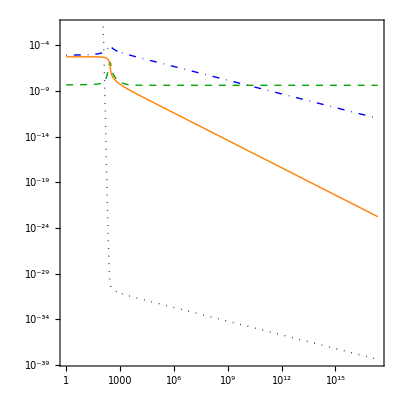

```mathematica
BackgroundPlot
```

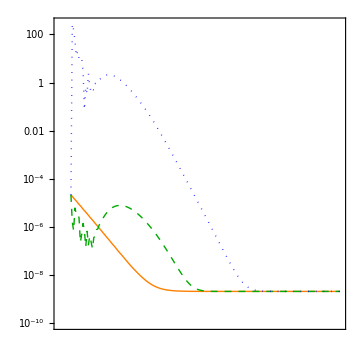

```mathematica
PerturbationsPlot
```